```mathematica
(* need to get sufficient coefficients to match, and need 0's in higher-order coefficients intead of abscent, so request many *)
```

```mathematica
mydBdx[x_]:=A+Sin[x/dx]/dx
mydBdxseries[x_]:=Normal[Series[mydBdx[x],{x,0,10}]]
myfulllist=CoefficientList[mydBdxseries[x],x]
(*myshortlist=Table[myfulllist[[i]],{i,1,7}]*)
myshortlist=Table[myfulllist[[i]],{i,1,5}]
```

{A,1/dx^2,0,-1/(6 dx^4),0,1/(120 dx^6),0,-1/(5040 dx^8),0,1/(362880 dx^10)}

{A,1/dx^2,0,-1/(6 dx^4),0}

```mathematica
myshortlist={A,1/dx^2,0,-1/(6 dx^4),0,F5/dx^6,F6/dx^7}
```

{A,1/dx^2,0,-1/(6 dx^4),0,F5/dx^6,F6/dx^7}

```mathematica
(* Seeing if can determine B^x along x-dir to one higher order than lowest order *)
(* Sasha would determine dBdx's polynomial coefficients for left and right cells centered on cell center, where point-valued dBx/dx is known from differencing a2c_i B^i across cell center *)
(* Here x/dx=0 is cell center, x/dx=1/2 is right cell face of interest and x/dx=-1/2 is the left cell face of interest *)
dBdxraw[x_]:=F0+F1/dx (x/dx-0) + F2 /dx(x/dx-0)^2+ F3 /dx(x/dx-0)^3+ F4 /dx(x/dx-0)^4+ F5 /dx(x/dx-0)^5+ F6 /dx(x/dx-0)^6;
```

```mathematica
(* set F's using function we want to fit *)
```

```mathematica
rawlist=CoefficientList[dBdxraw[x],x]
```

{F0,F1/dx^2,F2/dx^3,F3/dx^4,F4/dx^5,F5/dx^6,F6/dx^7}

```mathematica
solF=Solve[myshortlist ==rawlist,{F0,F1,F2,F3,F4,F5,F6}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{F0→A,F1→1,F2→0,F3→-1/6,F4→0}}

```mathematica
(* The dBdxraw has constraints, but let place them later through the use of the a2c_i function *)
```

```mathematica
(* Now form integral that is distribution of Bx in the left and right cell with Bxl0 and Bxr0 cell center point values of field *)
Bx[t_]:=Bx0+Integrate[Evaluate[dBdxraw[x]],{x,0*dx,t}]
```

```mathematica
(* Now setup equation that determines Bx0, that is a2c_i B^i = known quantity *)
(* We want to form a2c_i B^i, which requires forming another function f=a2c_i Bx such that c2a_i f=Bx *)
f[x_]:=f0+f1/dx (x/dx-0) + f2 /dx(x/dx-0)^2+ f3 /dx(x/dx-0)^3+ f4 /dx(x/dx-0)^4+ f5 /dx(x/dx-0)^5+ f6 /dx(x/dx-0)^6+ f7 /dx(x/dx-0)^7;
RunningAverage[t_]:=FullSimplify[Integrate[f[x],{x,t-dx/2,t+dx/2}]/dx];
```

```mathematica
(* Now obtain coefficients of f from those of Bx *)
```

```mathematica
sol=Solve[CoefficientList[RunningAverage[x],x] ==CoefficientList[Bx[x],x],{f0,f1,f2,f3,f4,f5,f6,f7}]
```

{{f0→(40320 Bx0-1680 F1+294 F3-155 F5)/40320,f1→(6720 dx^2 F0-560 dx F2+196 dx F4-155 dx F6)/6720,f2→1/96 (48 dx F1-12 dx F3+7 dx F5),f3→1/48 (16 dx F2-8 dx F4+7 dx F6),f4→1/24 (6 dx F3-5 dx F5),f5→1/20 (4 dx F4-5 dx F6),f6→(dx F5)/6,f7→(dx F6)/7}}

```mathematica
a2cBx[x_]:=f[x]//.sol[[1]]
```

```mathematica
(* stare at result *)
```

```mathematica
a2cBx[x]
```

(40320 Bx0-1680 F1+294 F3-155 F5)/40320+((6720 dx^2 F0-560 dx F2+196 dx F4-155 dx F6) x)/(6720 dx^2)+((48 dx F1-12 dx F3+7 dx F5) x^2)/(96 dx^3)+((16 dx F2-8 dx F4+7 dx F6) x^3)/(48 dx^4)+((6 dx F3-5 dx F5) x^4)/(24 dx^5)+((4 dx F4-5 dx F6) x^5)/(20 dx^6)+(F5 x^6)/(6 dx^6)+(F6 x^7)/(7 dx^7)

```mathematica
(* now have a2c_i B^i distribution that has to give back known a2c_i B^i's, use this to obtain Bxl0 and Bxr0 assuming rest will correctly give back correct distribution of B^i *)
```

```mathematica
fun1=FullSimplify[a2cBx[1/2*dx]]
fun2=FullSimplify[a2cBx[-1/2*dx]]
sol12=FullSimplify[Solve[{fun1==a2cright,fun2==a2cleft},{Bx0,F0}]]
FullSimplify[(fun1-fun2)/dx//.sol12[[1]]]
```

Bx0+(dx F0)/2+F1/12-F3/120+F5/252

Bx0-(dx F0)/2+F1/12-F3/120+F5/252

{{Bx0→1/120 (60 a2cleft+60 a2cright-10 F1+F3)-F5/252,F0→(-a2cleft+a2cright)/dx}}

(-a2cleft+a2cright)/dx

```mathematica
(* Get final Bxl and Bxr distributions *)
```

```mathematica
myBx[x_]:=FullSimplify[Bx[x]//.sol[[1]]]//.sol12[[1]]
```

```mathematica
(* Get final a2c_i B^i distributions *)
mya2cBx[x_]:=FullSimplify[a2cBx[x]//.sol[[1]]]//.sol12[[1]]
```

```mathematica
(* stare at solution *)
mya2cBx[x]
```

1/(40320 dx^7)(dx^7 (42 (-40 F1+7 F3+960 (1/120 (60 a2cleft+60 a2cright-10 F1+F3)-F5/252))-155 F5)+6 dx^6 (6720 (-a2cleft+a2cright)-560 F2+196 F4-155 F6) x+420 dx^5 (48 F1-12 F3+7 F5) x^2+840 dx^4 (16 F2-8 F4+7 F6) x^3+1680 dx^3 (6 F3-5 F5) x^4+2016 dx^2 (4 F4-5 F6) x^5+6720 dx F5 x^6+5760 F6 x^7)

```mathematica
(* Check how a2cB^i is set *)
```

```mathematica
FullSimplify[mya2cBx[1/2*dx]]
FullSimplify[mya2cBx[-1/2*dx]]
```

a2cright

a2cleft

```mathematica
(* We DO get back a2cB at the face! good. *)
```

```mathematica
(* Assume don't care if face point values are different *)
```

```mathematica
(* Get point values at faces just to see *)
```

```mathematica
Bpointright=FullSimplify[myBx[1/2*dx]]
Bpointleft=FullSimplify[myBx[-1/2*dx]]
```

a2cright+(1680 F1+1680 F2+966 F3+252 F4-55 F5+45 F6)/40320

a2cleft+(1680 F1-1680 F2+966 F3-252 F4-55 F5-45 F6)/40320

```mathematica
myFhigherorder=Solve[{Bpointleft==myBxl,Bpointright==myBxr},{F5,F6}][[1]]
```

{F5→42/55 (480 a2cleft+480 a2cright+40 F1+23 F3-480 myBxl-480 myBxr),F6→28/15 (240 a2cleft-240 a2cright-20 F2-3 F4-240 myBxl+240 myBxr)}

```mathematica
(* So generally point value mismatch at faces that can be fixed by adding higher-order terms *)
```

```mathematica
(* Try to force face point to be same as a2c value *)
```

```mathematica
//.{a2cleft->.5,a2cright->1.5}
```

```mathematica
fakeBx=Integrate[mydBdx[x],x]//.{A->F0,dx->1}//.{F0->(a2cright-a2cleft)/dx}//.{dx->1}
D[fakeBx,x]//.{x->0}
```

(-a2cleft+a2cright) x-Cos[x]

-a2cleft+a2cright

```mathematica
fakeBx//.{x->-1/2}
fakeBx//.{x->1/2}
```

-1.37758

-0.377583

{myBxl→a2cleft,myBxr→a2cright}

{dx→1,a2cleft→-1.37758,a2cright→-0.377583}

-0.877581+0.999997 x

{-1.0719+0.999997 x+x^2/2-x^4/24+(1519 x^6)/330}

{-0.962304+0.999997 x+x^2/2-x^4/24}

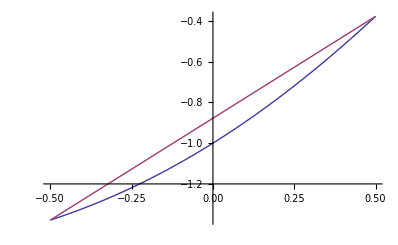

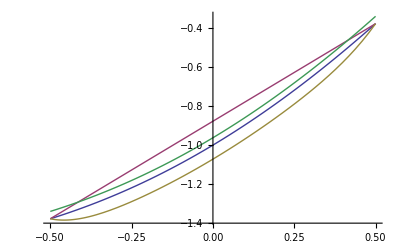

```mathematica
nocorrection={F1->0,F2->0,F3->0,F4->0,F5->0,F6->0};
weno5jon={myBxl->a2cleft,myBxr->a2cright}
weno5simple={dx->1,a2cleft->-1.37758,a2cright->-.377583}
toplotBxlinear=FullSimplify[myBx[x]//.nocorrection//.weno5simple]
toplotBxnonlinear=myBx[x]//.myFhigherorder//.solF//.weno5jon//.weno5simple
toplotBxnonlinear2=myBx[x]//.{F5->0,F6->0}//.solF//.weno5jon//.weno5simple
Plot[{fakeBx,toplotBxlinear},{x,-1/2,1/2}]
Plot[{fakeBx,toplotBxlinear,toplotBxnonlinear,toplotBxnonlinear2},{x,-1/2,1/2}]
```

```mathematica
myBx[x]
```

1/120 (60 a2cleft+60 a2cright-10 F1+F3)-F5/252+((-a2cleft+a2cright) x)/dx+(F1 x^2)/(2 dx^2)+(F2 x^3)/(3 dx^3)+(F3 x^4)/(4 dx^4)+(F4 x^5)/(5 dx^5)+(F5 x^6)/(6 dx^6)+(F6 x^7)/(7 dx^7)

```mathematica
(F5/6*(1./2)^6)//.FullSimplify[myFhigherorder//.solF//.weno5jon]
```

{0.0719223}

```mathematica
crap1=N[toplotBxnonlinear[[1]]//.{x->y-1/2.}]
crap2=N[toplotBxnonlinear[[1]]//.{x->y+1/2.}]
```

-1.06932+0.99 (-0.5+y)+0.5 (-0.5+y)^2-0.0416667 (-0.5+y)^4+4.60303 (-0.5+y)^6

-1.06932+0.99 (0.5+y)+0.5 (0.5+y)^2-0.0416667 (0.5+y)^4+4.60303 (0.5+y)^6

```mathematica
CoefficientList[crap1,y]
CoefficientList[crap2,y]
```

{-1.37,-0.352235,4.75284,-11.4242,17.2197,-13.8091,4.60303}

{-0.38,2.33223,4.75284,11.4242,17.2197,13.8091,4.60303}

```mathematica
(* so corrections F5/F6 are smaller than max of other coefficients, so consider the correction ok? *)
```

{{F0→A,F1→1,F2→0,F3→-1/6,F4→0}}

```mathematica
(* so fake coefficients are always larger than set coefficients?  That's crappy *)
```

```mathematica
CoefficientList[toplotBxnonlinear,x]
CoefficientList[toplotBxnonlinear2,x]
```

{{-1.06932,0.99,1/2,0,-1/24,0,1519/330}}

{{-0.959722,0.99,1/2,0,-1/24}}

```mathematica
solF
myFhigherorder//.weno5jon//.solF
```

{{F0→A,F1→1,F2→0,F3→-1/6,F4→0}}

{{F5→1519/55,F6→0}}

```mathematica
(* perhaps instead of forcing Bpoint=Bhat, one can choose higher order F5,F6 so that first guess of point values on a face is averaged and this is the value to choose to set F5,F6 by *)
```